```mathematica
CatNext[n_]:=(3n+1)CatalanNumber[n]
```

```mathematica
Nk[k_]:=Round[4^(k+3)/3-3(k+3)/2]
```

```mathematica
Nk /@ Range[-1,10]
```

{2,17,79,334,1356,5451,21833,87368,349510,1398085,5592387,22369602}

```mathematica
CatalanNumber/@Range[0,10]
```

{1,1,2,5,14,42,132,429,1430,4862,16796}

```mathematica
k=7
n=Nk[k]
a=CatNext[n-1.]
x=CatalanNumber[n+k+2.]
y=CatalanNumber[n+k+3.]
b=CatNext[n+0.]
a<x<y<b
{a/x, y/b}
```

7

349510

6.95544942246004×10^210422

6.9554693229594×10^210422

2.78217578947865×10^210423

2.78217578670461×10^210423

False

{0.99999713887037,1.00000000099707}

```mathematica
N[CatalanNumber[349520]]
CatalanNumber[N[349520]]
```

2.78217579327451×10^210423

2.78217578947865×10^210423

```mathematica
k=12
n=Nk[k]
a=CatNext[n-1];
x=CatalanNumber[n+k+2];
y=CatalanNumber[n+k+3];
b=CatNext[n+0];
a<x<y<b
{a/x, y/b}
```

12

357913919

True

{611660300806385361077455858638973329311845271338963012795839223643442331197466518073850830035432421930994013176071277068100/611660301660864573368500423632385902993526925153143327501219615947694591187898164999442789289707603267877940648563412845833,27728601504051483872144366001738272837550388034138568135429722957815086468310460985145168629993885928992407634104841908007336/27728601542787908921246379353547461386147036219822988169482213994766675043251639131036069962517059039292118282882787740367485}

```mathematica
k=13
n=Nk[k]
a=CatNext[n-1];
x=CatalanNumber[n+k+2];
y=CatalanNumber[n+k+3];
b=CatNext[n+0];
a<x<y<b
{a/x, y/b}
```

13

1431655741

```mathematica
CatNext[16.]
CatalanNumber[19.]
CatalanNumber[20.]
CatNext[17.]
```

1.73253×10^9

1.76726×10^9

6.56412×10^9

6.74153×10^9

```mathematica
CatNext[n-k-1.]/CatalanNumber[n+2.]
CatalanNumber[n+3.]/CatNext[n-k+0.]
```

0.988791

0.999497

```mathematica
Mod[CatalanNumber[80000],10^8]
```

32067040

```mathematica
Nk2[k_]:=4^k/3-(3/2)k-1/3
```

```mathematica
Nk2/@Range[15]
```

{-1/2,2,33/2,79,667/2,1356,10901/2,21833,174735/2,349510,2796169/2,5592387,44739203/2,89478464,715827837/2}

```mathematica
CatProd[n_,k_]:=Product[2(2i+1)/(i+2),{i,n,n+k-1}]
CatProdK[k_]:=CatProd[Nk2[k],k]
```

```mathematica
3 16+1
CatProd[16,3]//N
CatProd[17,3]//N
3 17+1
```

49

49.9825

50.6316

52

```mathematica
Nk2[14]
```

89478464

```mathematica
k=14;
n=Nk2[k];
3(n-1)+1
N[CatProd[n-1,k],20]
N[CatProd[n,k],20]
3n+1
4^k-9/2k
1/(3n+1-CatProd[n,k])/n^(3/4)//N
```

268435390

2.6843539299999712501×10^8

2.6843539299999782909×10^8

268435393

268435393

0.50069

```mathematica
k=13;
n=Ceiling[Nk2[k]]
N[3(n-1)+1,20]
N[CatProd[n-1,k],20]
N[CatProd[n,k],20]
N[3n+1,20]
N[4^k-9/2k,20]
```

22369602

6.7108804×10^7

6.7108805499991282821×10^7

6.7108805499993897976×10^7

6.7108807×10^7

6.71088055×10^7

```mathematica
k=16;
n=Nk2[k];
3(n-1)+1
N[CatProd[n-1,k],20]
N[CatProd[n,k],20]
3n+1
4^k-9/2k
1/(3n+1-CatProd[n,k])/n^(3/4)//N
```

4294967221

4.2949672239999997695×10^9

4.2949672239999998198×10^9

4294967224

4294967224

0.753945

```mathematica
k=18;
n=Nk2[k];
3(n-1)+1
N[CatProd[n-1,k],20]
N[CatProd[n,k],20]
3n+1
4^k-9/2k
1/(3n+1-CatProd[n,k])/n^(3/4)//N
```

68719476652

6.8719476654999999982×10^10

6.8719476654999999986×10^10

68719476655

68719476655

1.17622

```mathematica
k=20;
n=Nk2[k];
3(n-1)+1
N[CatProd[n-1,k],30]
N[CatProd[n,k],30]
3n+1
4^k-9/2k
1/(3n+1-CatProd[n,k])/n^(4/5)//N
```

1099511627683

1.09951162768599999999862893674×10^12

1.09951162768599999999887450031×10^12

1099511627686

1099511627686

0.498186

```mathematica
k=22;
n=Nk2[k];
3(n-1)+1
N[CatProd[n-1,k],30]
N[CatProd[n,k],30]
3n+1
3n+1==4^k-9/2k
1/(3n+1-CatProd[n,k])/n^(4/5)//N
```

17592186044314

1.75921860443169999999998972982×10^13

1.75921860443169999999999141806×10^13

17592186044317

True

0.710978

```mathematica
k=24;
n=Nk2[k];
3(n-1)+1
N[CatProd[n-1,k],30]
N[CatProd[n,k],30]
3n+1
3n+1==4^k-9/2k
1/(3n+1-CatProd[n,k])/n^(4/5)//N
```

281474976710545

2.81474976710547999999999992422×10^14

2.81474976710547999999999993573×10^14

281474976710548

True

1.03311

```mathematica
k=2000;
n=Nk2[k];
3n<CatProd[n,k]<3n+1
3n+1==4^k-9/2k
1/(3n+1-CatProd[n,k])//N
```

True

True

9.77261861500097×10^1196

```mathematica
Nk2[2000]//N
```

4.39401364476981×10^1203

```mathematica
CatProd[Nk2[50],50]//FullSimplify
```

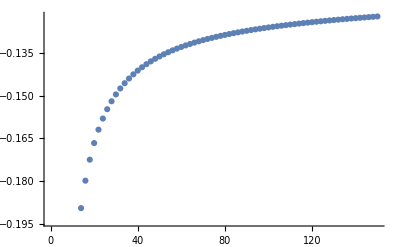

```mathematica
ListPlot[(
{#,((Log[3Nk2[#]+1-CatProdK[#]]+Log[Nk2[#]]-2Log[Log[Nk2[#]]]+.5355)*Log[Nk2[#]]-(1/1000)Log[Log[Nk2[#]]])}
)&/@Range[4,150,2]]
```

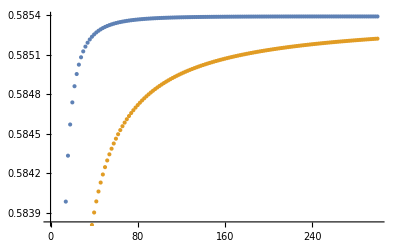

```mathematica
ListPlot[{
(
{#,(3Nk2[#]+1-CatProdK[#])/(Log[Nk2[#]]^2/Nk2[#])+.05/(#-3)}
)&/@Range[4,300,2],

(
{#,(3Nk2[#]+1-CatProdK[#])/(Log[Nk2[#]]^2/Nk2[#])}
)&/@Range[4,300,2]
}]
```

```mathematica
(500^2/(4^500)) / (Log[Nk2[500]]^2/Nk2[500])//N
```

0.173999

```mathematica
27/8/(3Log[4]^2)//FullSimplify
```

9/(8 Log[4]^2)

```mathematica
3375/1000
```

27/8

```mathematica
Log[Nk2[50.]]
```

68.2161

```mathematica
Log[4^50/3.]
```

68.2161

```mathematica
.5854/.179
```

3.27039

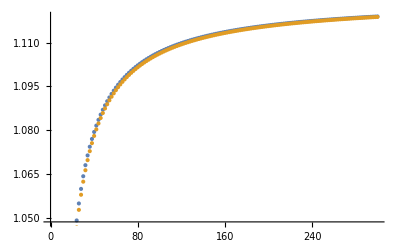

```mathematica
ListPlot[{
(
{#,(3Nk2[#]+1-CatProdK[#])/(#^2/Nk2[#])+.05/(#-3)}
)&/@Range[4,300,2],

(
{#,(3Nk2[#]+1-CatProdK[#])/(#^2/Nk2[#])}
)&/@Range[4,300,2]
}]
```

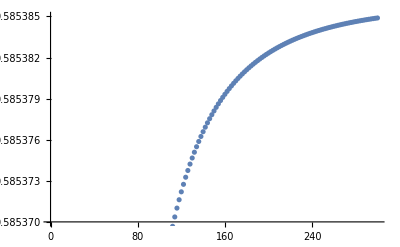

```mathematica
ListPlot[{
(
{#,(3Nk2[#]+1-CatProdK[#])/(Log[Nk2[#]]^2/Nk2[#])+(1/20.5)/(#-3)}
)&/@Range[4,300,2]
},PlotRange->{.58537,.585385}]
```

```mathematica
,

(
{#,(CatProdK[#]-3Nk2[#]-1+((27/8)#^2/4^#)(1-1.5/#))/((27/8)#^2/4^#)}
)&/@Range[4,300,2],

(
{#,(CatProdK[#]-3Nk2[#]-1+((27/8)#^2/4^#)(1-0/#))/((27/8)#^2/4^#)}
)&/@Range[4,300,2]
```

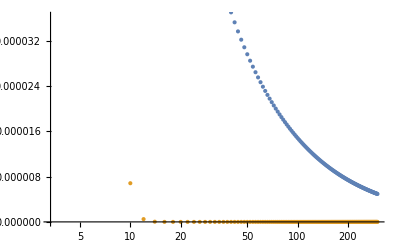

```mathematica
ListLogLinearPlot[{
(
{#,(CatProdK[#]-3Nk2[#]-1+((27/8)#^2/4^#)-(5.62#/4^#))/((27/8)#^2/4^#)}
)&/@Range[4,300,2],
(
{#,(CatProdK[#]-3Nk2[#]-1+((27/8)#^2/4^#)-(45/8#/4^#))/((27/8)#^2/4^#)}
)&/@Range[4,300,2]
}]
```

General::munfl: 1.025370406767889×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.097205268837029×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.636894889588827×10^-313 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

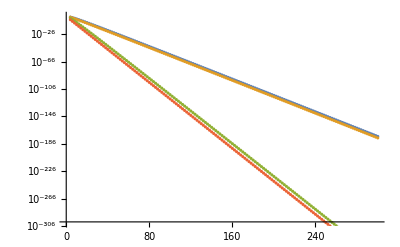

```mathematica
ListLogPlot[{
(
{#,-(CatProdK[#]-3Nk2[#]-1)}
)&/@Range[4,300,2],
(
{#,(CatProdK[#]-3Nk2[#]-1+((27/8)#^2/4^#))}
)&/@Range[4,300,2],
(
{#,(CatProdK[#]-3Nk2[#]-1+((27/8)#^2/4^#)-(45/8#/4^#))}
)&/@Range[4,300,2],
({#, 16^-#}&/@Range[4,300,2])
},PlotRange->{10^-300,1}]
```

```mathematica
?Nk2
```

```mathematica
?CatProd
```

```mathematica
(CatProdK[#]-3Nk2[#]-1+((27/8)#^2/4^#)-(45/8#/4^#))&[150]//N
```

1.41787×10^-174

```mathematica
1/16^150//N
```

2.40992×10^-181

```mathematica
%%/%
```

5.88347×10^6

```mathematica
150^3 / %900
```

0.573641

```mathematica
1/%
```

1.74325

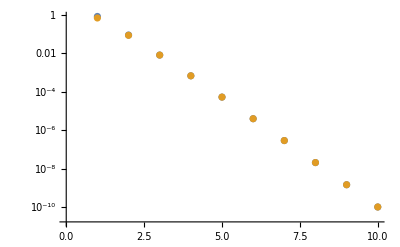

```mathematica
ListLogPlot[{CatProdK[#]-3Nk2[#]-1+(27/8)#^2/4^#&/@Range[2,20,2],
(45/8#/4^#)&/@Range[2,20,2]}]
```

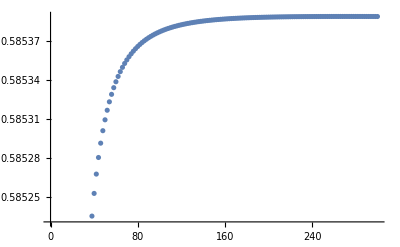

```mathematica
ListPlot[{
(
{#,(3Nk2[#]+1-CatProdK[#])/(Log[Nk2[#]]^2/Nk2[#])+(1/20)/(#-3)}
)&/@Range[4,300,2]
}]
```

```mathematica
Exp[Exp[.5854]]
```

6.02374

```mathematica
1/.5854
```

1.70823

```mathematica
Differences[(3Nk2[#]+1-CatProdK[#])/(Log[Nk2[#]]^2/Nk2[#])&/@Range[4,300]][[-1]]//N
% * 300^2
```

5.66469×10^-7

0.0509822

```mathematica
1/.05098
```

19.6155

```mathematica
1/.5853
```

1.70853

```mathematica
1/(3Sqrt[5]-5)//FullSimplify
```

1/(-5+3 √5)

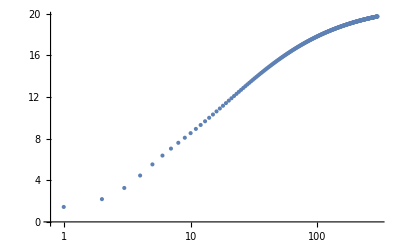

```mathematica
ListLogLinearPlot[{1/((Differences[(3Nk2[#]+1-CatProdK[#])/(Log[Nk2[#]]^2/Nk2[#])&/@Range[4,301]])*(#^2&/@Range[4,300]))},PlotRange->Full]
```

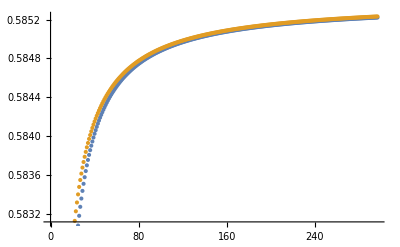

```mathematica
ListPlot[{N[(3Nk2[#]+1-CatProdK[#])/(Log[Nk2[#]]^2/Nk2[#])&/@Range[4,300]],
.5854-.05/(#-3)&/@Range[4,300]}
]
```

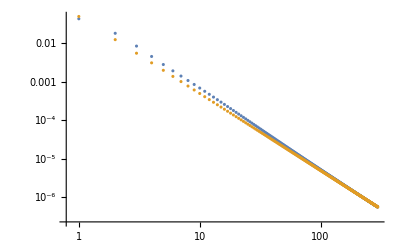

```mathematica
ListLogLogPlot[{N[Differences[(3Nk2[#]+1-CatProdK[#])/(Log[Nk2[#]]^2/Nk2[#])&/@Range[4,300]]],
.05/(#-3)^2&/@Range[4,300]}
]
```

```mathematica
{#,(3Nk2[#]+1-CatProdK[#])/(Log[Nk2[#]]^2/Nk2[#])}&[2000]//N
```

{2000.,0.585361}

```mathematica
Exp[-.5355]
```

0.585377

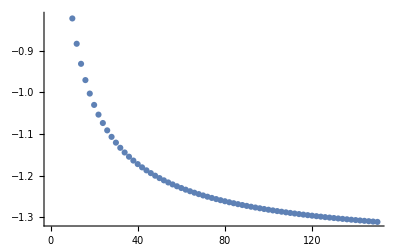

```mathematica
ListPlot[(
{#,(Log[4^#-9/2#-CatProdK[#]])/#}
)&/@Range[4,150,2]]
```

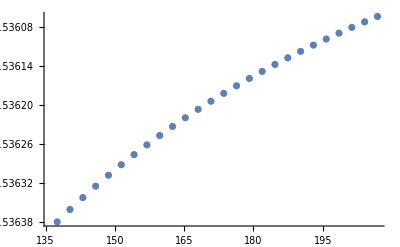

```mathematica
ListPlot[(
{Log[Nk2[#]],(Log[3Nk2[#]+1-CatProdK[#]]+Log[Nk2[#]]-2Log[Log[Nk2[#]]])}
)&/@Range[100,150,2]]
```

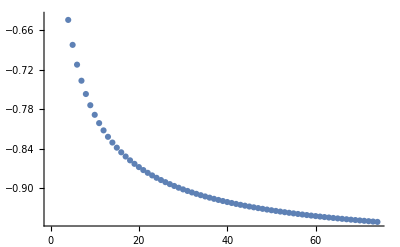

```mathematica
ListPlot[(
Log[3Nk2[#]+1-CatProdK[#]]/Log[Nk2[#]]
)&/@Range[4,150,2]]
```

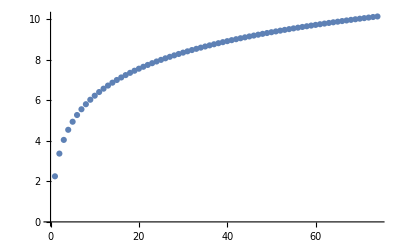

```mathematica
ListPlot[Log[3Nk2[#]+1-CatProdK[#]]+Log[Nk2[#]]&/@Range[4,150,2]]
```

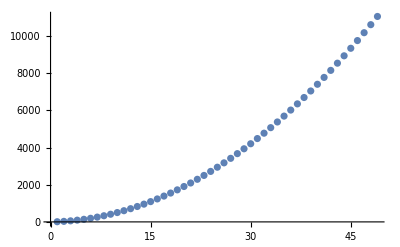

```mathematica
ListPlot[(3Nk2[#]+1-CatProdK[#])Nk2[#]&/@Range[4,100,2]]
```

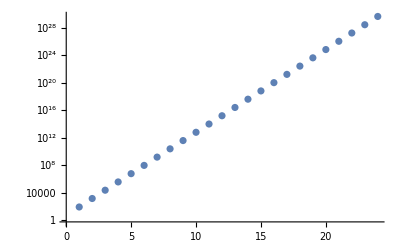

```mathematica
ListLogPlot[Nk2/@Range[4,50,2]]
```